```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/DESI/math

```mathematica
Union1s=Import["Union1s.csv"];
Union2s=Import["Union2s.csv"];
Pantheon1s=Import["Pantheon1s.csv"];
Pantheon2s=Import["Pantheon2s.csv"];
DESY1s=Import["DESY1s.csv"];
DESY2s=Import["DESY2s.csv"];
```

Import::nffil: File Union1s.csv not found during Import.

Import::nffil: File Union2s.csv not found during Import.

Import::nffil: File Pantheon1s.csv not found during Import.

Import::nffil: File Pantheon2s.csv not found during Import.

Import::nffil: File DESY1s.csv not found during Import.

```mathematica
Union1sMean=Mean[Union1s];
Union2sMean=Mean[Union2s];
Pantheon1sMean=Mean[Pantheon1s];
Pantheon2sMean=Mean[Pantheon2s];
DESY1sMean=Mean[DESY1s];
DESY2sMean=Mean[DESY2s];
```

```mathematica
Union1spol=Sort[Table[{Norm[Union1s[[i]]-Union1sMean],ArcTan[(Union1s[[i]]-Union1sMean)[[1]],(Union1s[[i]]-Union1sMean)[[2]]]},{i,Length[Union1s]}],#1[[2]]<#2[[2]]&];
Union2spol=Sort[Table[{Norm[Union2s[[i]]-Union2sMean],ArcTan[(Union2s[[i]]-Union2sMean)[[1]],(Union2s[[i]]-Union2sMean)[[2]]]},{i,Length[Union2s]}],#1[[2]]<#2[[2]]&];
Pantheon1spol=Sort[Table[{Norm[Pantheon1s[[i]]-Pantheon1sMean],ArcTan[(Pantheon1s[[i]]-Pantheon1sMean)[[1]],(Pantheon1s[[i]]-Pantheon1sMean)[[2]]]},{i,Length[Pantheon1s]}],#1[[2]]<#2[[2]]&];
Pantheon2spol=Sort[Table[{Norm[Pantheon2s[[i]]-Pantheon2sMean],ArcTan[(Pantheon2s[[i]]-Pantheon2sMean)[[1]],(Pantheon2s[[i]]-Pantheon2sMean)[[2]]]},{i,Length[Pantheon2s]}],#1[[2]]<#2[[2]]&];
DESY1spol=Sort[Table[{Norm[DESY1s[[i]]-DESY1sMean],ArcTan[(DESY1s[[i]]-DESY1sMean)[[1]],(DESY1s[[i]]-DESY1sMean)[[2]]]},{i,Length[DESY1s]}],#1[[2]]<#2[[2]]&];
DESY2spol=Sort[Table[{Norm[DESY2s[[i]]-DESY2sMean],ArcTan[(DESY2s[[i]]-DESY2sMean)[[1]],(DESY2s[[i]]-DESY2sMean)[[2]]]},{i,Length[DESY2s]}],#1[[2]]<#2[[2]]&];
```

```mathematica
Union1ssorted=Join[Table[{Union1spol[[i,1]]Cos[Union1spol[[i,2]]],Union1spol[[i,1]]Sin[Union1spol[[i,2]]]}+Union1sMean,{i,Length[Union1spol]}],{{Union1spol[[1,1]]Cos[Union1spol[[1,2]]],Union1spol[[1,1]]Sin[Union1spol[[1,2]]]}+Union1sMean}];
Union2ssorted=Join[Table[{Union2spol[[i,1]]Cos[Union2spol[[i,2]]],Union2spol[[i,1]]Sin[Union2spol[[i,2]]]}+Union2sMean,{i,Length[Union2spol]}],{{Union2spol[[1,1]]Cos[Union2spol[[1,2]]],Union2spol[[1,1]]Sin[Union2spol[[1,2]]]}+Union2sMean}];
Pantheon1ssorted=Join[Table[{Pantheon1spol[[i,1]]Cos[Pantheon1spol[[i,2]]],Pantheon1spol[[i,1]]Sin[Pantheon1spol[[i,2]]]}+Pantheon1sMean,{i,Length[Pantheon1spol]}],{{Pantheon1spol[[1,1]]Cos[Pantheon1spol[[1,2]]],Pantheon1spol[[1,1]]Sin[Pantheon1spol[[1,2]]]}+Pantheon1sMean}];
Pantheon2ssorted=Join[Table[{Pantheon2spol[[i,1]]Cos[Pantheon2spol[[i,2]]],Pantheon2spol[[i,1]]Sin[Pantheon2spol[[i,2]]]}+Pantheon2sMean,{i,Length[Pantheon2spol]}],{{Pantheon2spol[[1,1]]Cos[Pantheon2spol[[1,2]]],Pantheon2spol[[1,1]]Sin[Pantheon2spol[[1,2]]]}+Pantheon2sMean}];
DESY1ssorted=Join[Table[{DESY1spol[[i,1]]Cos[DESY1spol[[i,2]]],DESY1spol[[i,1]]Sin[DESY1spol[[i,2]]]}+DESY1sMean,{i,Length[DESY1spol]}],{{DESY1spol[[1,1]]Cos[DESY1spol[[1,2]]],DESY1spol[[1,1]]Sin[DESY1spol[[1,2]]]}+DESY1sMean}];
DESY2ssorted=Join[Table[{DESY2spol[[i,1]]Cos[DESY2spol[[i,2]]],DESY2spol[[i,1]]Sin[DESY2spol[[i,2]]]}+DESY2sMean,{i,Length[DESY2spol]}],{{DESY2spol[[1,1]]Cos[DESY2spol[[1,2]]],DESY2spol[[1,1]]Sin[DESY2spol[[1,2]]]}+DESY2sMean}];
```

```mathematica
Export["Union1s_sorted.dat",Union1ssorted];
Export["Union2s_sorted.dat",Union2ssorted];
Export["Pantheon1s_sorted.dat",Pantheon1ssorted];
Export["Pantheon2s_sorted.dat",Pantheon2ssorted];
Export["DESY1s_sorted.dat",DESY1ssorted];
Export["DESY2s_sorted.dat",DESY2ssorted];
```

```mathematica
Union1ssorted=Import["Union1s_sorted.dat"];
Union2ssorted=Import["Union2s_sorted.dat"];
Pantheon1ssorted=Import["Pantheon1s_sorted.dat"];
Pantheon2ssorted=Import["Pantheon2s_sorted.dat"];
DESY1ssorted=Import["DESY1s_sorted.dat"];
DESY2ssorted=Import["DESY2s_sorted.dat"];
```

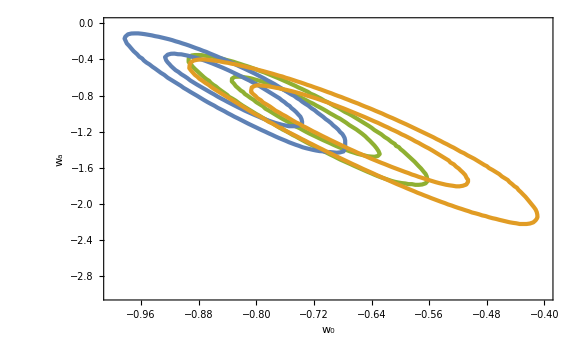

```mathematica
ListPlot[{DESY1ssorted,DESY2ssorted,Pantheon1ssorted,Pantheon2ssorted,Union1ssorted,Union2ssorted},FrameLabel->{Subscript[w, 0],Subscript[w, a]},PlotRange->{{-1,-0.4},{-3,0}},PlotStyle->{{AbsoluteThickness[3],Color[3]},{AbsoluteThickness[3],Color[3]},{AbsoluteThickness[3],Color[1]},{AbsoluteThickness[3],Color[1]},{AbsoluteThickness[3],Color[2]},{AbsoluteThickness[3],Color[2]}}]
```

### w/o DM

```mathematica
DESY2s=Import["DESY2s.csv"];
```

```mathematica
DESY2sMean=Mean[DESY2s]
```

{-0.723974,-1.06981}

```mathematica
DESY2spol=Sort[Table[{Norm[DESY2s[[i]]-DESY2sMean],ArcTan[(DESY2s[[i]]-DESY2sMean)[[1]],(DESY2s[[i]]-DESY2sMean)[[2]]]},{i,Length[DESY2s]}],#1[[2]]<#2[[2]]&];
```

```mathematica
DESY2ssorted=Table[{DESY2spol[[i,1]]Cos[DESY2spol[[i,2]]],DESY2spol[[i,1]]Sin[DESY2spol[[i,2]]]}+DESY2sMean,{i,Length[DESY2spol]}];
```

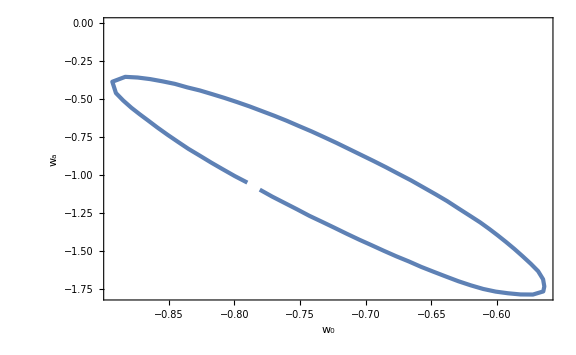

```mathematica
ListPlot[DESY2ssorted,FrameLabel->{Subscript[w, 0],Subscript[w, a]}]
```

```mathematica
e1[w0_]=3/2(1+w0);
e2[w0_,wa_]=-wa/(1+w0);
beta[w0_,wa_]=-e1[w0]+1/2 e2[w0,wa];
```

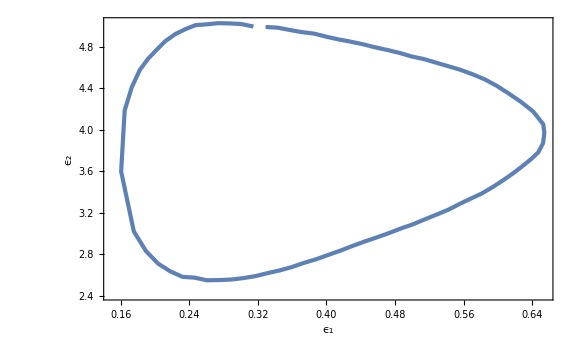

```mathematica
ListPlot[Map[{e1[#[[1]]],e2[#[[1]],#[[2]]]}&,DESY2ssorted],FrameLabel->{Subscript[ϵ, 1],Subscript[ϵ, 2]}]
```

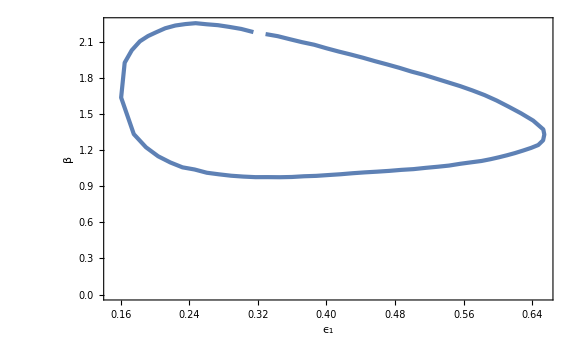

```mathematica
ListPlot[Map[{e1[#[[1]]],beta[#[[1]],#[[2]]]}&,DESY2ssorted],FrameLabel->{Subscript[ϵ, 1],β}]
```

```mathematica
H[x_]=A Cos[Sqrt[β/2]x];
```

```mathematica
V[x_]=3 H[x]^2-2 H'[x]^2//FullSimplify
```

1/2 A^2 (3-β+(3+β) Cos[√2 x √β])

```mathematica
eH[x_]=2(H'[x]/H[x])^2//FullSimplify
```

β Tan[(x √β)/(√2)]^2

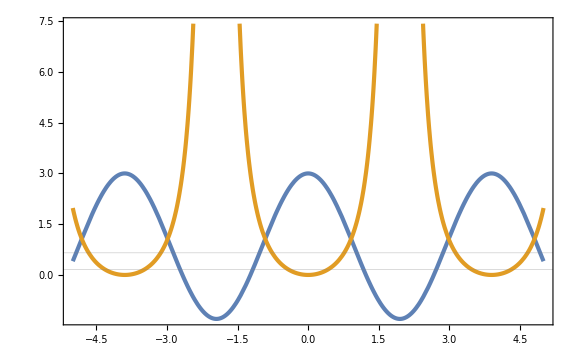

```mathematica
Plot[{V[x]/.{β->1.3,A->1},eH[x]/.{β->1.3}},{x,-5,5},GridLines->{None,{Min[e1[DESY2ssorted[[All,1]]]],Max[e1[DESY2ssorted[[All,1]]]]}}]
```

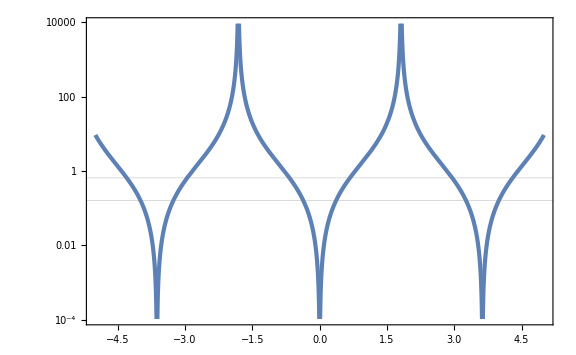

```mathematica
LogPlot[eH[x]/.{β->1.5,A->1},{x,-5,5},GridLines->{None,{Min[e1[DESY2ssorted[[All,1]]]],Max[e1[DESY2ssorted[[All,1]]]]}}]
```

```mathematica
x0=x/.Solve[eH[x]==e10,x][[2]]/.{C[1]->0}
```

(√2 ArcTan[(√e10)/(√β)])/(√β)

```mathematica
p0=Sqrt[2e10];
```

```mathematica
As=A/.Solve[p0^2/2+V[x0]/H0^2==3(1-Ωm),A][[2]]
```

(√2 H0 √(3-e10-3 Ωm))/(√(3-β+(3+β) Cos[2 ArcTan[(√e10)/(√β)]]))

```mathematica
Ωs[x_,p_]=1/3(p^2/2+V[x]/H0^2)/.{A->As}
Htot[z_,x_,p_]=Sqrt[Ωm (1+z)^3(*+Ωr H0^2(1+z)^4*)+Ωs[x,p]]//Simplify
```

1/3 (p^2/2+((3-e10-3 Ωm) (3-β+(3+β) Cos[√2 x √β]))/(3-β+(3+β) Cos[2 ArcTan[(√e10)/(√β)]]))

(√(p^2+6 (1+z)^3 Ωm-(2 (-3+e10+3 Ωm) (3-β+(3+β) Cos[√2 x √β]))/(3-β+(3+β) Cos[2 ArcTan[(√e10)/(√β)]])))/(√6)

```mathematica
Htot[0,x0,p0]//Simplify
```

1

```mathematica
pc=3086/1000 10^16(*m*);
H0s=(68 10^3)/(10^6 pc);
H0s//N
```

2.2035×10^-18

```mathematica
t0=H0s 138 10^8 60 60 24 36525/100;
t0//N
```

0.959613

```mathematica
ti=10^-4;
xi=28/100;
EoM=Simplify[{x''[t]+3Htot[z[t],x[t],x'[t]]x'[t]+V'[x[t]]/H0^2==0/.{A->As}(*,x[t0]==x0*),x[ti]==xi,x'[ti]==0(*8907/10000 p0*),
z'[t]==-Htot[z[t],x[t],x'[t]](1+z[t]),z[t0]==0}/.{β->15/10,e10->4/10,Ωm->3/10}]
```

{969 √3 Sin[√3 x[t]]==2 √390 x'[t] √(791+969 Cos[√3 x[t]]+1404 z[t]+1404 z[t]^2+468 z[t]^3+260 x'[t]^2)+520 x''[t],25 x[1/10000]==7,x'[1/10000]==0,z'[t]==-((1+z[t]) √(791+969 Cos[√3 x[t]]+1404 z[t]+1404 z[t]^2+468 z[t]^3+260 x'[t]^2))/(2 √390),z[46271331/48218750]==0}

```mathematica
sol=NDSolve[EoM,{x[t],x'[t],z[t]},{t,ti,t0}(*,WorkingPrecision->30*)][[1]]
```

{x[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t]}

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
zsol[t_]=z[t]/.sol;
Hsol[t_]=Htot[zsol[t],xsol[t],psol[t]]/.{β->15/10,e10->4/10,Ωm->3/10};
esol[t_]=psol[t]^2/(2 Hsol[t]^2);
Ωssol[t_]=Ωs[xsol[t],psol[t]]/.{β->15/10,e10->4/10,Ωm->3/10};
wsol[t_]=(1/3(psol[t]^2/2-V[xsol[t]]/H0^2/.{A->As}))/Ωssol[t]/.{β->15/10,e10->4/10,Ωm->3/10};
wasol[t_]=(1+zsol[t])^2/zsol'[t] wsol'[t];
```

```mathematica
{wsol[t0],wasol[t0]}
```

{-0.809321,-0.671206}

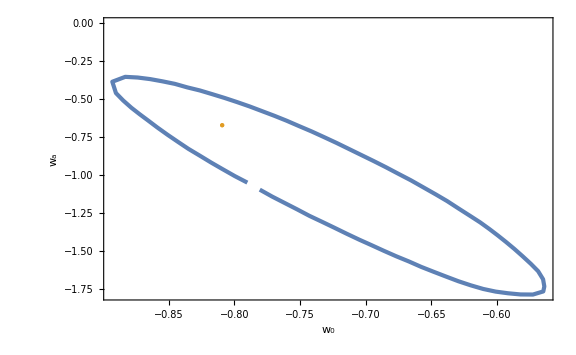

```mathematica
Show[ListPlot[DESY2ssorted,FrameLabel->{Subscript[w, 0],Subscript[w, a]}],ListPlot[{{wsol[t0],wasol[t0]}},PlotStyle->Directive[Color[2],PointSize[Large]],Joined->False]]
```

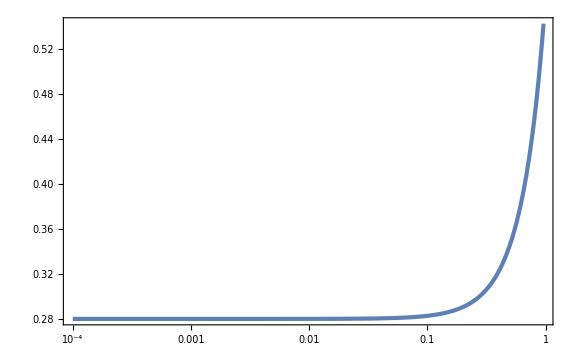

```mathematica
LogLinearPlot[xsol[t],{t,ti,t0},PlotRange->Full]
```

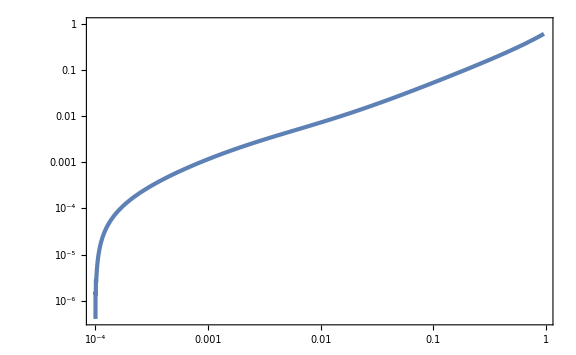

```mathematica
LogLogPlot[psol[t],{t,ti,t0}]
```

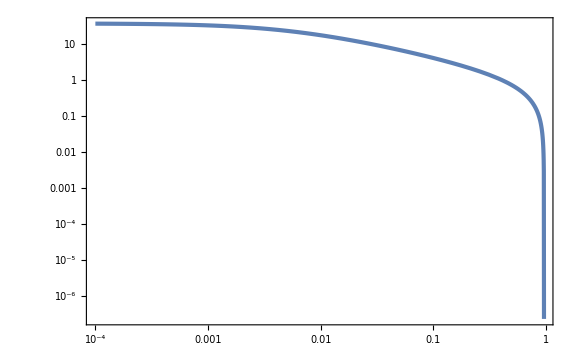

```mathematica
LogLogPlot[zsol[t],{t,ti,t0},PlotRange->Full]
```

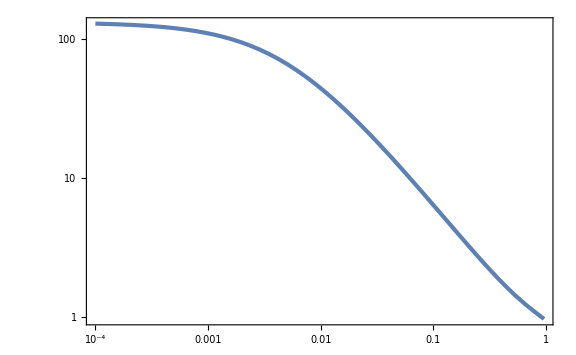

```mathematica
LogLogPlot[Hsol[t],{t,ti,t0}]
```

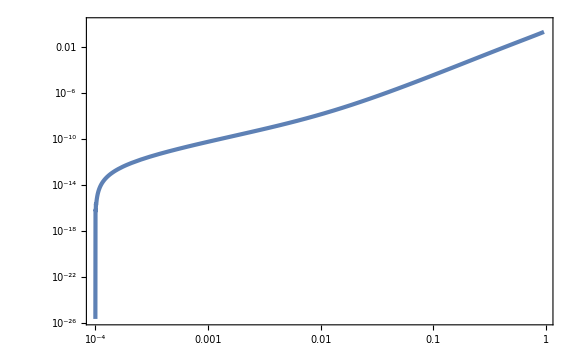

```mathematica
LogLogPlot[esol[t],{t,ti,t0}]
```

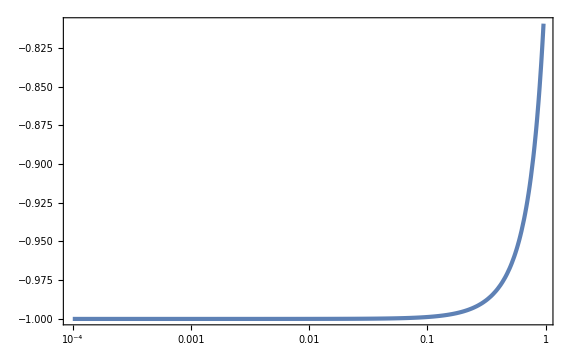

```mathematica
LogLinearPlot[wsol[t],{t,ti,t0},PlotRange->Full]
```

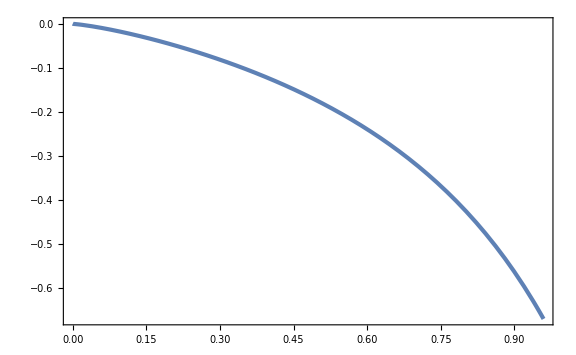

```mathematica
Plot[wasol[t],{t,ti,t0}]
```

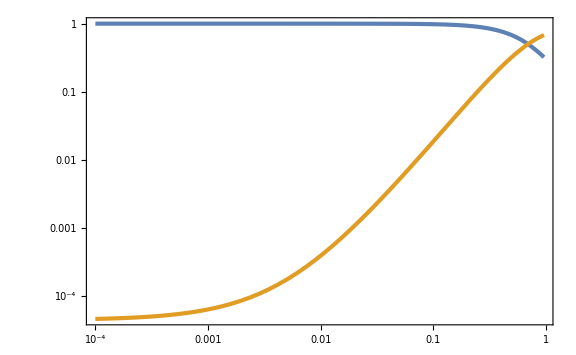

```mathematica
LogLogPlot[{(Ωm(1+zsol[t])^3)/(Ωm(1+zsol[t])^3+Ωs[xsol[t],psol[t]])/.{β->15/10,e10->4/10,Ωm->3/10},Ωs[xsol[t],psol[t]]/(Ωm(1+zsol[t])^3+Ωs[xsol[t],psol[t]])/.{β->15/10,e10->4/10,Ωm->3/10}},{t,ti,t0}]
```

### w/ DM

```mathematica
DESY2s=Import["DESY2s.csv"];
```

```mathematica
DESY2sMean=Mean[DESY2s]
```

{-0.723974,-1.06981}

```mathematica
DESY2spol=Sort[Table[{Norm[DESY2s[[i]]-DESY2sMean],ArcTan[(DESY2s[[i]]-DESY2sMean)[[1]],(DESY2s[[i]]-DESY2sMean)[[2]]]},{i,Length[DESY2s]}],#1[[2]]<#2[[2]]&];
```

```mathematica
DESY2ssorted=Table[{DESY2spol[[i,1]]Cos[DESY2spol[[i,2]]],DESY2spol[[i,1]]Sin[DESY2spol[[i,2]]]}+DESY2sMean,{i,Length[DESY2spol]}];
```

```mathematica
ListPlot[DESY2ssorted,FrameLabel->{Subscript[w, 0],Subscript[w, a]}]
```

-Graphics-

```mathematica
e10[w0_]=3/2(1+w0+R0)/(1+R0);
eϕ0[w0_]=3/2(1+w0)/(1+R0);
eM0[w0_]=3/2 R0/(1+R0);
```

```mathematica
eϕ0[w0]+eM0[w0]-e10[w0]//Simplify
```

0

```mathematica
-2/3(2eϕ0[w0](β+e10[w0])+(3w0)/(1+R0)eM0[w0])(1+R0)+(1-2/3 e10[w0])3w0 R0//Simplify
```

-((1+w0) (3+3 w0+2 β))

```mathematica
-2/3 e10[w0](2β+2e10[w0])/.{R0->0}
```

-((1+w0) (3 (1+w0)+2 β))

```mathematica
beta[w0_,wa_]=-wa/(2(1+w0))-3/2(1+w0);
```

```mathematica
-(1+w0)(3+3w0+2beta[w0,wa])//Simplify
```

wa

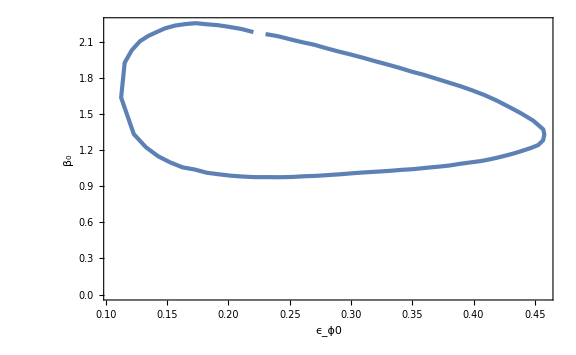

```mathematica
ListPlot[Map[{eϕ0[#[[1]]]/.{R0->3/7},beta[#[[1]],#[[2]]]/.{R0->3/7}}&,DESY2ssorted],FrameLabel->{Subscript[ϵ, ϕ0],Subscript[β, 0]}]
```

### V, V’

```mathematica
$Assumptions={1-w0>0,1+w0>0,V0>0,Vp0<0,H0>0,Mp>0,1-Ωm>0,xc>0};
```

```mathematica
p[t_]=x'[t]^2/2-V[x[t]];
ρ[t_]=x'[t]^2/2+V[x[t]];
```

```mathematica
w[t_]=p[t]/ρ[t]
```

(-V[x[t]]+1/2 x'[t]^2)/(V[x[t]]+1/2 x'[t]^2)

```mathematica
p0sol=Solve[w[0]==w0/.{V[x[0]]->V0,x'[0]->p0},p0][[2]]//Simplify
```

{p0→√2 √(-(V0 (1+w0))/(-1+w0))}

```mathematica
3 Mp^2 H0^2==p0^2/2+V0+3 Mp^2 Ωm H0^2/.p0sol//Simplify
```

2 V0==3 H0^2 Mp^2 (-1+w0) (-1+Ωm)

```mathematica
V0sol={V0->3/2 H0^2 Mp^2(1-w0)(1-Ωm)};
```

```mathematica
3 Mp^2 H0^2==p0^2/2+V0+3 Mp^2 Ωm H0^2/.p0sol/.V0sol//Simplify
```

True

```mathematica
wa==-w'[0]/H0/.{x''[0]->-3H0 p0-Vp0,V'[x[0]]->Vp0,V[x[0]]->V0,x'[0]->p0}/.p0sol/.V0sol//Simplify
```

wa==3-3 w0^2+(2 Vp0 √((1+w0)/(3-3 Ωm)))/(H0^2 Mp)

```mathematica
Vp0sol={Vp0->3/2 H0^2 Mp Sqrt[(1-Ωm)/(3(1+w0))](wa-3(1-w0^2))}
```

{Vp0→1/2 √3 H0^2 Mp (-3 (1-w0^2)+wa) √((1-Ωm)/(1+w0))}

```mathematica
wa==-w'[0]/H0/.{x''[0]->-3H0 p0-Vp0,V'[x[0]]->Vp0,V[x[0]]->V0,x'[0]->p0}/.p0sol/.V0sol/.Vp0sol//Simplify
```

True

```mathematica
V0norm[w0_]=V0/(Mp^2 H0^2)/.V0sol/.{Ωm->3/10}
```

(21 (1-w0))/20

```mathematica
Vpnorm[w0_,wa_]=Vp0/(Mp H0^2)/.Vp0sol/.{Ωm->3/10}
```

1/2 √(21/10) √(1/(1+w0)) (-3 (1-w0^2)+wa)

```mathematica
p0norm[w0_]=p0/(Mp H0)/.p0sol/.V0sol/.{Ωm->3/10}//Simplify
```

√(21/10) √(1+w0)

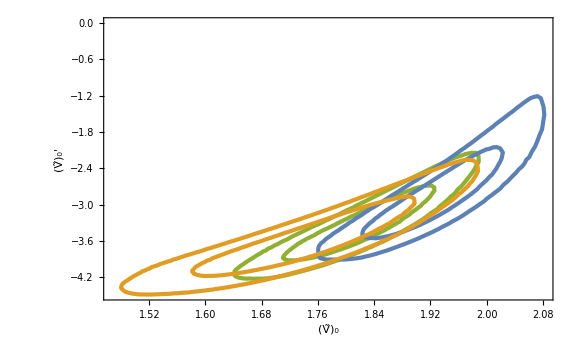

```mathematica
ListPlot[{Map[{V0norm[#[[1]]],Vpnorm[#[[1]],#[[2]]]}&,DESY1ssorted],Map[{V0norm[#[[1]]],Vpnorm[#[[1]],#[[2]]]}&,DESY2ssorted],Map[{V0norm[#[[1]]],Vpnorm[#[[1]],#[[2]]]}&,Pantheon1ssorted],Map[{V0norm[#[[1]]],Vpnorm[#[[1]],#[[2]]]}&,Pantheon2ssorted],Map[{V0norm[#[[1]]],Vpnorm[#[[1]],#[[2]]]}&,Union1ssorted],Map[{V0norm[#[[1]]],Vpnorm[#[[1]],#[[2]]]}&,Union2ssorted]},FrameLabel->{Subscript[OverTilde[V], 0],Subscript[OverTilde[V], 0]'},PlotStyle->{{AbsoluteThickness[3],Color[3]},{AbsoluteThickness[3],Color[3]},{AbsoluteThickness[3],Color[1]},{AbsoluteThickness[3],Color[1]},{AbsoluteThickness[3],Color[2]},{AbsoluteThickness[3],Color[2]}}]
```

```mathematica
m2[w0_,wa_]=Vpnorm[w0,wa]^2/(2V0norm[w0])//Simplify
```

-((-3+3 w0^2+wa)^2)/(4 (-1+w0^2))

```mathematica
KK[w0_,wa_]=Sqrt[1-4/3 m2[w0,wa]/V0norm[w0]]//Simplify
```

√(1-(20 (-3+3 w0^2+wa)^2)/(63 (-1+w0)^2 (1+w0)))

```mathematica
F[a_]=Sqrt[1+(1/(1-Ωm)-1)a^-3]/.{Ωm->3/10}//Simplify
```

√(1+3/(7 a^3))

```mathematica
calF[a_,w0_,wa_]=(((KK[w0,wa]-F[a])(F[a]+1)^KK[w0,wa]+(KK[w0,wa]+F[a])(F[a]-1)^KK[w0,wa])/((KK[w0,wa]-1/Sqrt[1-Ωm])(1/Sqrt[1-Ωm]+1)^KK[w0,wa]+(KK[w0,wa]+1/Sqrt[1-Ωm])(1/Sqrt[1-Ωm]-1)^KK[w0,wa]))^2/.{Ωm->3/10}//Simplify
```

((1+√(1+3/(7 a^3)))^(√(1-(20 (-3+3 w0^2+wa)^2)/(63 (-1+w0)^2 (1+w0)))) (-√(1+3/(7 a^3))+√(1-(20 (-3+3 w0^2+wa)^2)/(63 (-1+w0)^2 (1+w0))))+(-1+√(1+3/(7 a^3)))^(√(1-(20 (-3+3 w0^2+wa)^2)/(63 (-1+w0)^2 (1+w0)))) (√(1+3/(7 a^3))+√(1-(20 (-3+3 w0^2+wa)^2)/(63 (-1+w0)^2 (1+w0)))))^2/((1+√(10/7))^(√(1-(20 (-3+3 w0^2+wa)^2)/(63 (-1+w0)^2 (1+w0)))) (-√(10/7)+√(1-(20 (-3+3 w0^2+wa)^2)/(63 (-1+w0)^2 (1+w0))))+(-1+√(10/7))^(√(1-(20 (-3+3 w0^2+wa)^2)/(63 (-1+w0)^2 (1+w0)))) (√(10/7)+√(1-(20 (-3+3 w0^2+wa)^2)/(63 (-1+w0)^2 (1+w0)))))^2

```mathematica
ww[a_,w0_,wa_]=-1+(1+w0)a^(3(KK[w0,wa]-1))calF[a,w0,wa];
```

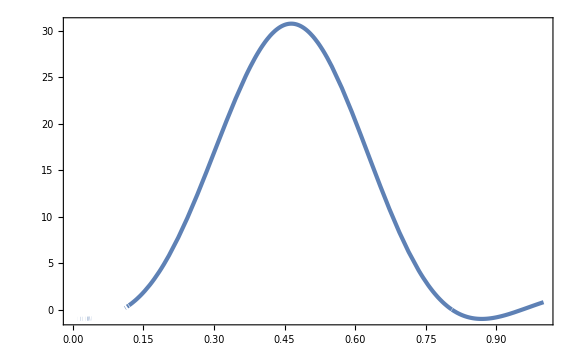

```mathematica
Plot[ww[a,0.8,-1],{a,0,1}]
```

```mathematica
V2[x_]=1/2 m2 x^2/.{m2->Vpnorm[w0,wa]^2/(2V0norm[w0])}//Simplify
x0norm[w0_,wa_]=2 V0norm[w0]/Vpnorm[w0,wa]//Simplify
```

-((-3+3 w0^2+wa)^2 x^2)/(8 (-1+w0^2))

-(√(42/5) (-1+w0) √(1+w0))/(-3+3 w0^2+wa)

```mathematica
Hnorm[z_,x_,p_]=Sqrt[Ωm(1+z)^3+(p^2/2+V2[x])/3]/.{Ωm->3/10};
```

```mathematica
w0s=-0.8;
was=-1;
ti=-1;
sol=NDSolve[{x''[t]+3Hnorm[z[t],x[t],x'[t]]x'[t]+V2'[x[t]]==0/.{w0->w0s,wa->was},
x[0]==x0norm[w0s,was],x'[0]==p0norm[w0s],
z'[t]==-Hnorm[z[t],x[t],x'[t]](1+z[t])/.{w0->w0s,wa->was},z[0]==0},{z[t],x[t],x'[t]},{t,ti,0},WorkingPrecision->30][[1]]
```

NDSolve::precw: The precision of the differential equation ({{3.00444 x[t]+3 x'[t] √(Times[«2»]+Times[«2»])+x''[t]==0,x[0]==-1.12167,x'[0]==0.648074,z'[t]==-((1+z[t]) √(3/10 Power[«2»]+1/3 Plus[«2»])),z[0]==0},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::ndsz: At t == -0.78994285292711544780710981767, step size is effectively zero; singularity or stiff system suspected.

{z[t]→InterpolatingFunction[{{-0.789942852927115447807109817670, 0}}, <>][t],x[t]→InterpolatingFunction[{{-0.789942852927115447807109817670, 0}}, <>][t],x'[t]→InterpolatingFunction[{{-0.789942852927115447807109817670, 0}}, <>][t]}

```mathematica
zsol[t_]=z[t]/.sol;
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
```

InterpolatingFunction::dmval: Input value {-0.99998} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-0.99998} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-0.979571} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-0.979571} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-0.959163} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-0.959163} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

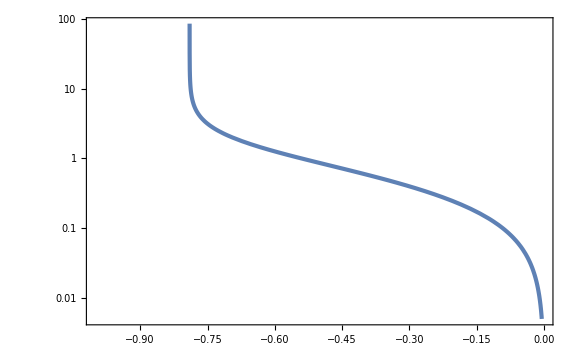

```mathematica
LogPlot[zsol[t],{t,ti,0}]
```

InterpolatingFunction::dmval: Input value {-0.99998} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-0.99998} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-0.979571} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-0.979571} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-0.959163} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-0.959163} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

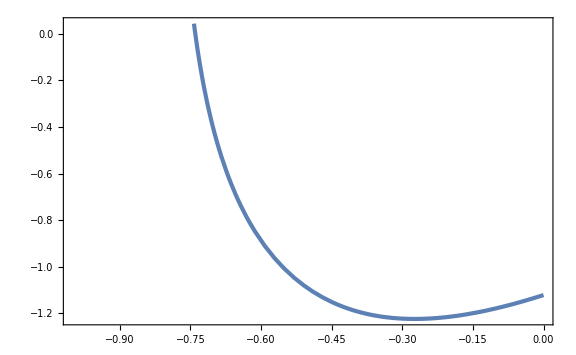

```mathematica
Plot[xsol[t],{t,ti,0}]
```

```mathematica
Vcos[x_]=Λ2 f^2(1+Cos[x/f])/.{Λ2->(1+Cos[xc])/Sin[xc]^2 Vp0^2/V0,f->-V0/Vp0 Sin[xc]/(1+Cos[xc])}//Simplify
```

(V0 (1+Cos[(Vp0 x Cot[xc/2])/V0]))/(1+Cos[xc])

```mathematica
Vcos[xc f]/.{f->-V0/Vp0 Sin[xc]/(1+Cos[xc])}//Simplify
Vcos'[xc f]/.{f->-V0/Vp0 Sin[xc]/(1+Cos[xc])}//Simplify
```

V0

Vp0

```mathematica
Hnorm[z_,x_,p_]=Sqrt[Ωm(1+z)^3+(p^2/2+Vcos[x])/3]/.{Ωm->3/10};
```

```mathematica
xcs=0.98301925;
w0s=-0.8;
was=-1;
ti=-1;
sol=NDSolve[{x''[t]+3Hnorm[z[t],x[t],x'[t]]x'[t]+Vcos'[x[t]]==0/.{xc->xcs,V0->V0norm[w0s],Vp0->Vpnorm[w0s,was]},
x[0]==xcs f/.{f->-V0/Vp0 Sin[xc]/(1+Cos[xc])}/.{xc->xcs,V0->V0norm[w0s],Vp0->Vpnorm[w0s,was]},x'[0]==x0norm[w0s],
z'[t]==-Hnorm[z[t],x[t],x'[t]](1+z[t])/.{xc->xcs,V0->V0norm[w0s],Vp0->Vpnorm[w0s,was]},z[0]==0},{z[t],x[t],x'[t]},{t,ti,0},WorkingPrecision->30][[1]]
```

NDSolve::precw: The precision of the differential equation ({{-4.04961 Sin[3.33078 x[«1»]]+3 x'[t] √(Times[«2»]+Times[«2»])+x''[t]==0,x[0]==0.295132,x'[0]==0.648074,z'[t]==-((1+z[t]) √(3/10 Power[«2»]+1/3 Plus[«2»])),z[0]==0},{},{},{},{}}) is less than WorkingPrecision (30.).

NDSolve::ndsz: At t == -0.951784525853786200455918728721, step size is effectively zero; singularity or stiff system suspected.

{z[t]→InterpolatingFunction[{{-0.951784525853786200455918728721, 0}}, <>][t],x[t]→InterpolatingFunction[{{-0.951784525853786200455918728721, 0}}, <>][t],x'[t]→InterpolatingFunction[{{-0.951784525853786200455918728721, 0}}, <>][t]}

```mathematica
zsol[t_]=z[t]/.sol;
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
```

InterpolatingFunction::dmval: Input value {-0.99998} lies outside the range of data in the interpolating function. Extrapolation will be used.

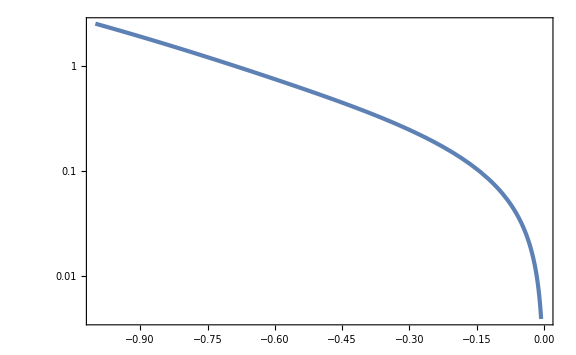

```mathematica
LogPlot[zsol[t],{t,ti,0}]
```

InterpolatingFunction::dmval: Input value {-0.99998} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-0.99998} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-0.979571} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-0.979571} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-0.959163} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-0.959163} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

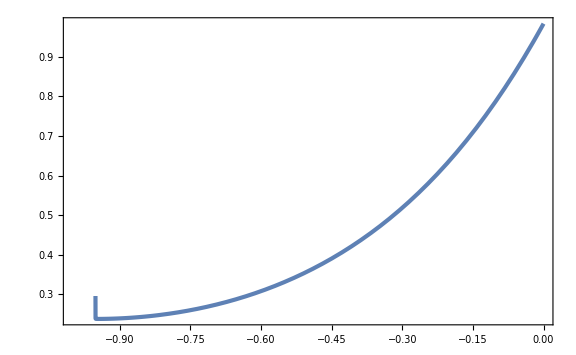

```mathematica
Plot[xsol[t]/f/.{f->-V0/Vp0 Sin[xc]/(1+Cos[xc])}/.{xc->xcs,V0->V0norm[w0s],Vp0->Vpnorm[w0s,was]},{t,ti,0}]
```

InterpolatingFunction::dmval: Input value {-0.99998} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-0.99998} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-0.979571} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {-0.979571} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {-0.959163} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-0.959163} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

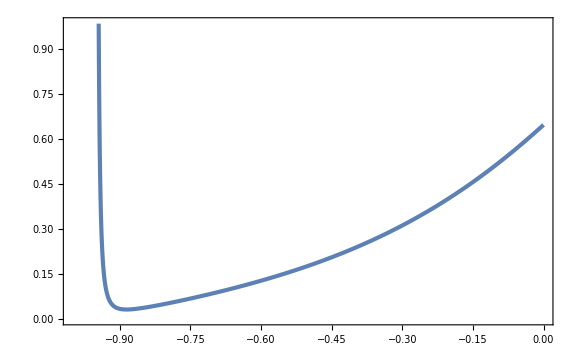

```mathematica
Plot[psol[t],{t,ti,0}]
```

### Thawing

```mathematica
$Assumptions={Ωϕ>0,1-Ωϕ>0,KK>0,a>0};
```

```mathematica
F[a_]=Sqrt[1+(Ωϕ^-1-1)a^-3];
calF[a_]=(((KK-F[a])(F[a]+1)^KK+(KK+F[a])(F[a]-1)^KK)/((KK-Ωϕ^(-1/2))(Ωϕ^(-1/2)+1)^KK+(KK+Ωϕ^(-1/2))(Ωϕ^(-1/2)-1)^KK))^2;
w[a_]=-1+(1+w0)a^(3(KK-1))calF[a];
```

```mathematica
(1+w[a])/a/.{Ωϕ->7/10}//Simplify
```

(a^(-4+3 KK) ((1+√(1+3/(7 a^3)))^KK (-√(1+3/(7 a^3))+KK)+(-1+√(1+3/(7 a^3)))^KK (√(1+3/(7 a^3))+KK))^2 (1+w0))/(((1+√(10/7))^KK (-√(10/7)+KK)+(-1+√(10/7))^KK (√(10/7)+KK))^2)

```mathematica
Integrate[(1+w[a])/a/.{Ωϕ->7/10}//Simplify,a]
```

((1+w0) ∫a^(-4+3 KK) ((1+√(1+3/(7 a^3)))^KK (-√(1+3/(7 a^3))+KK)+(-1+√(1+3/(7 a^3)))^KK (√(1+3/(7 a^3))+KK))^2ⅆa)/(((1+√(10/7))^KK (-√(10/7)+KK)+(-1+√(10/7))^KK (√(10/7)+KK))^2)

```mathematica
w[1]//Simplify
```

w0

```mathematica
wa[KK_,w0_]=-w'[1]/.{Ωϕ->7/10}//Simplify
```

(3 (13 √70 ((-7+√70)^KK-(7+√70)^KK)+140 ((-7+√70)^KK+(7+√70)^KK) KK+7 √70 ((-7+√70)^KK-(7+√70)^KK) KK^2) (1+w0))/(10 (√70 ((-7+√70)^KK-(7+√70)^KK)+7 ((-7+√70)^KK+(7+√70)^KK) KK))

```mathematica
wa[KK,-0.99]//Simplify
```

(0.326297 (-7+√70)^KK-0.326297 (7+√70)^KK+0.42 (-7+√70)^KK KK+0.42 (7+√70)^KK KK+0.175699 (-7+√70)^KK KK^2-0.175699 (7+√70)^KK KK^2)/(8.3666 (-7+√70)^KK-8.3666 (7+√70)^KK+7. (-7+√70)^KK KK+7. (7+√70)^KK KK)

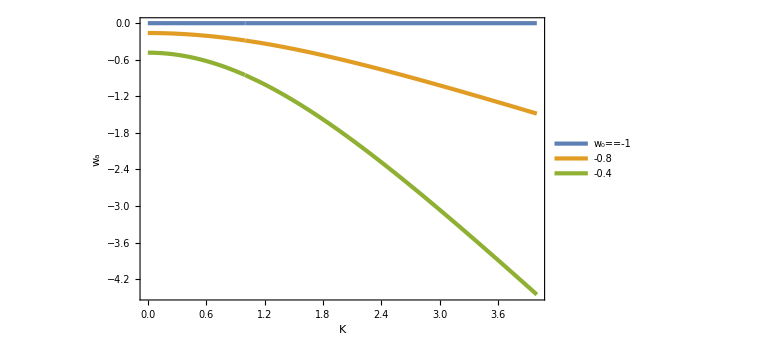

```mathematica
Plot[{wa[KK,-1],wa[KK,-0.8],wa[KK,-0.4]},{KK,0,4},FrameLabel->{K,Subscript[w, a]},PlotLegends->Placed[{Subscript[w, 0]==-1,-0.8,-0.4},{0.2,0.25}]]
```

```mathematica
w[a]/.{KK->0.5,Ωϕ->7/10}//Simplify
```

-1+(12.6608 ((-1+√(1+3/(7 a^3)))^0.5 (0.5+√(1+3/(7 a^3)))+(0.5-√(1+3/(7 a^3))) (1+√(1+3/(7 a^3)))^0.5)^2 (1+w0))/a^1.5

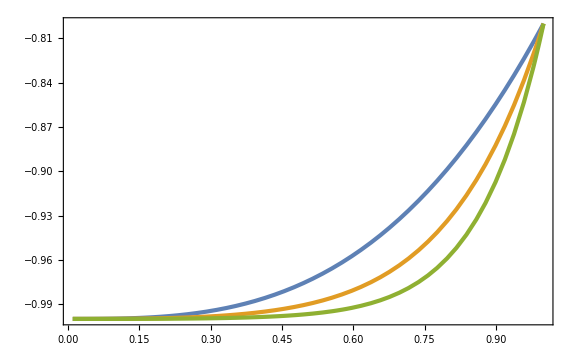

```mathematica
Plot[{w[a]/.{KK->2,Ωϕ->7/10,w0->-0.8},w[a]/.{KK->3,Ωϕ->7/10,w0->-0.8},w[a]/.{KK->4,Ωϕ->7/10,w0->-0.8}},{a,0.01,1}]
```

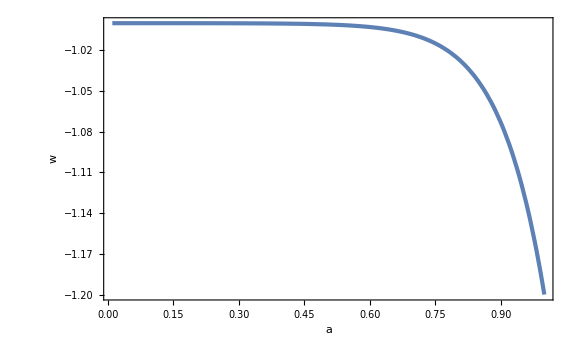

```mathematica
Plot[w[a]/.{KK->5,Ωϕ->7/10,w0->-1.2},{a,0.01,1},PlotRange->Full,FrameLabel->{{w,None},{a,Row[{K==5,",  ",Subscript[w, 0]==-1.2}]}}]
```

```mathematica
wim[a_]=-1+(1+w0)a^-3((Kp Cos[Kp ArcSinh[Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]]]-F[a]Sin[Kp ArcSinh[Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]]])/(Kp Cos[Kp ArcSinh[Sqrt[Ωϕ/(1-Ωϕ)]]]-Ωϕ^(-1/2)Sin[Kp ArcSinh[Sqrt[Ωϕ/(1-Ωϕ)]]]))^2;
```

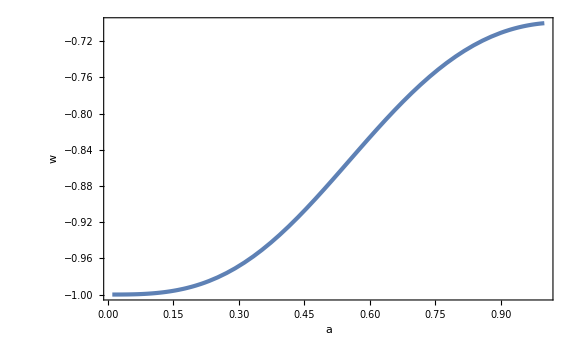

```mathematica
Plot[wim[a]/.{Kp->1,Ωϕ->7/10,w0->-0.7},{a,0.01,1},FrameLabel->{{w,None},{a,Row[{K'==1,",  ",Subscript[w, 0]==-0.7}]}}]
```

```mathematica
waim[Kp_,w0_]=-wim'[1]/.{Ωϕ->7/10}//Simplify
```

(3 (1+w0) (140 Kp Cos[Kp ArcSinh[√(7/3)]]+√70 (-13+7 Kp^2) Sin[Kp ArcSinh[√(7/3)]]))/(70 Kp Cos[Kp ArcSinh[√(7/3)]]-10 √70 Sin[Kp ArcSinh[√(7/3)]])

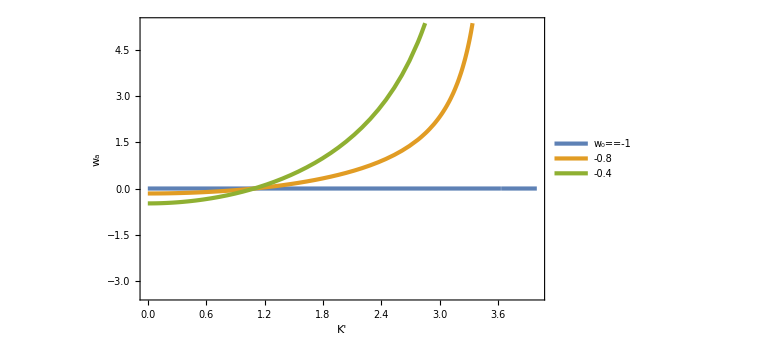

```mathematica
Plot[{waim[Kp,-1],waim[Kp,-0.8],waim[Kp,-0.4]},{Kp,0,4},FrameLabel->{K',Subscript[w, a]},PlotLegends->Placed[{Subscript[w, 0]==-1,-0.8,-0.4},{0.2,0.75}]]
```

```mathematica
Kdiv08=Kp/.FindRoot[1/waim[Kp,-0.8]==0,{Kp,4}]
```

3.63199

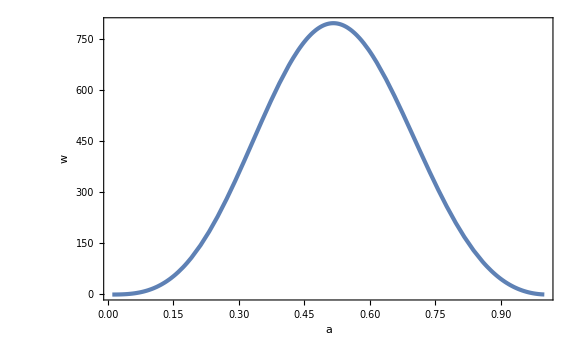

```mathematica
Plot[wim[a]/.{Kp->3.6,Ωϕ->7/10,w0->-0.8},{a,0.01,1},FrameLabel->{{w,None},{a,Row[{K'==3.6,",  ",Subscript[w, 0]==-0.8}]}}]
```

```mathematica
V[x_]=Λ2 f^2(1+Cos[x/f]);
```

```mathematica
Kcf[xc_,f_]=Sqrt[1-4/3 V''[xc f]/V[xc f]]
```

√(1+(4 Cos[xc])/(3 f^2 (1+Cos[xc])))

```mathematica
fK[KK_]=f/.Solve[Kcf[xc,f]==KK,f][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(2 √Cos[xc])/(√3 √(-1+KK^2-Cos[xc]+KK^2 Cos[xc]))

```mathematica
Hnorm[z_,x_,p_]=Sqrt[Ωm(1+z)^3+(p^2/2+V[x])/3]/.{Ωm->3/10};
```

```mathematica
w0s=-0.7;
Ks=KK/.FindRoot[wa[KK,w0s]==-1,{KK,5}]
xcs=0.55(*0.6*)(*0.7*)(*0.3*)(*0.5*);
Λ2s=8.7(*7.5*)(*5.7*)(*25*)(*10.3*);
fs=0.41(*fK[Ks]/.{xc->xcs}*)
tf=2;
```

2.17103

0.41

```mathematica
Sqrt[1-4/3 V''[xcs fs]/V[xcs fs]]/.{f->fs}
```

2.15643

```mathematica
sol=NDSolve[{x''[t]+3Hnorm[z[t],x[t],x'[t]]x'[t]+V'[x[t]]==0/.{f->fs,Λ2->Λ2s},
x[0]==xcs fs,x'[0]==0,
z'[t]==-Hnorm[z[t],x[t],x'[t]](1+z[t])/.{f->fs,Λ2->Λ2s},z[0]==1000},{z[t],x[t],x'[t]},{t,0,tf}][[1]]
```

{z[t]→InterpolatingFunction[…][t],x[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t]}

```mathematica
zsol[t_]=z[t]/.sol;
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
wsol[t_]=(psol[t]^2/2-V[xsol[t]])/(psol[t]^2/2+V[xsol[t]])/.{f->fs,Λ2->Λ2s};
```

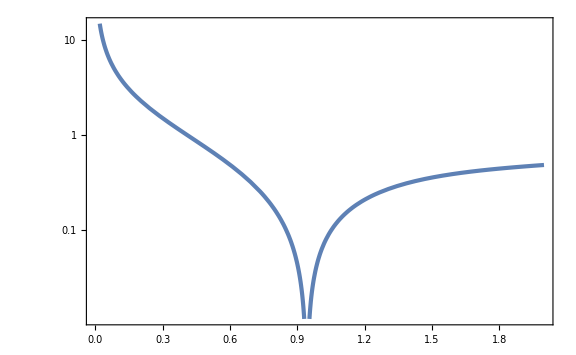

```mathematica
LogPlot[Abs[zsol[t]],{t,0,tf}]
```

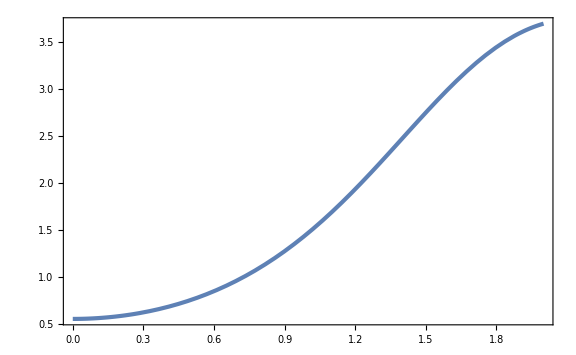

```mathematica
Plot[xsol[t]/fs,{t,0,tf}]
```

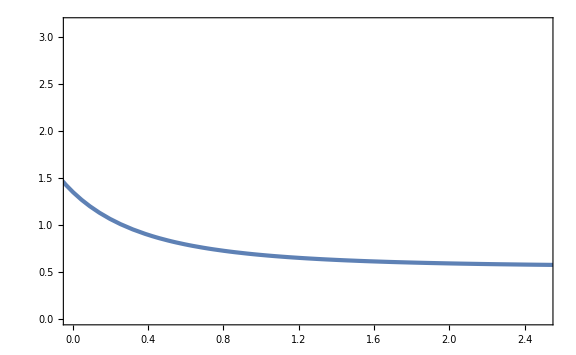

```mathematica
ParametricPlot[{zsol[t],xsol[t]/fs},{t,0,tf},PlotRange->{{0,2.5},{0,π}}]
```

```mathematica
t0=t/.FindRoot[zsol[t]==0,{t,0.8}]
```

0.942556

```mathematica
xsol[t0]-xcs fs
```

0.32848

```mathematica
Hnorm[zsol[t0],xsol[t0],psol[t0]]/.{f->fs,Λ2->Λ2s,Ωm->3/10}
```

0.998769

```mathematica
Λ2s
Λ2s/Hnorm[zsol[t0],xsol[t0],psol[t0]]^2/.{f->fs,Λ2->Λ2s,Ωm->3/10}
```

8.7

8.72145

```mathematica
Ωm/Hnorm[zsol[t0],xsol[t0],psol[t0]]^2/.{f->fs,Λ2->Λ2s,Ωm->3/10}
```

0.30074

```mathematica
wsol[t0]
```

-0.702258

```mathematica
pad={{100,50},{70,30}};
```

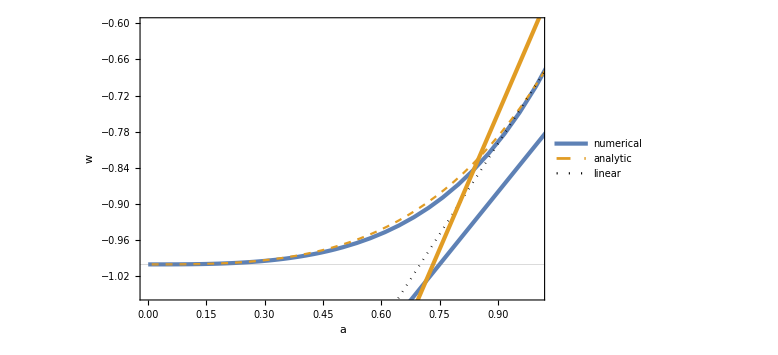

```mathematica
Show[Plot[{1,1,1},{x,0,1},PlotRange->{{0,1},{-1.05,-0.6}},FrameLabel->{a,w},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[2],Dashed},{Black,Dotted}},PlotLegends->Placed[LineLegend[{"numerical","analytic","linear"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.25,0.75}],GridLines->{None,{-1}},ImagePadding->pad],
ParametricPlot[{1/(1+zsol[t]),wsol[t]},{t,0,tf}],
Plot[w[a]/.{Ωϕ->7/10,KK->Sqrt[1-4/3 V''[xcs fs]/V[xcs fs]]}/.{f->fs,Λ2->Λ2s,w0->w0s},{a,0.01,1.2},PlotStyle->{Color[2],Dashed},PlotRange->Full],
Plot[-0.7-1(1-a),{a,0,1.2},PlotStyle->{Black,Dotted}],
Plot[{-0.8-0.8(1-a),-0.6-1.5(1-a)},{a,0,1.2}]]
```

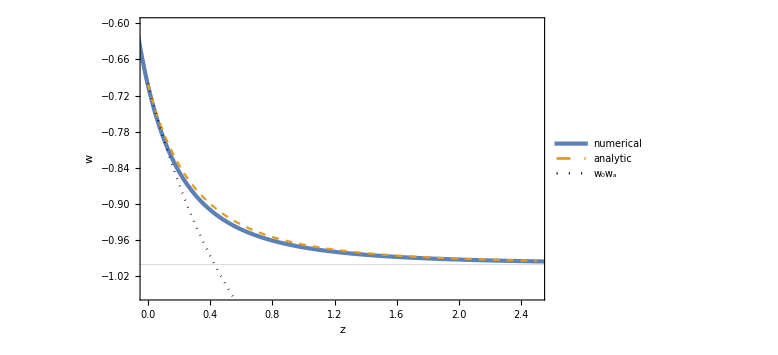

```mathematica
Show[Plot[{1,1,1},{x,0,1},PlotRange->{{0,2.5},{-1.05,-0.6}},FrameLabel->{z,w},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[2],Dashed},{Black,Dotted}},PlotLegends->Placed[LineLegend[{"numerical","analytic","w_0w_a"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.75,0.75}],GridLines->{None,{-1}},ImagePadding->pad],
ParametricPlot[{zsol[t],wsol[t]},{t,0,tf}],
Plot[w[1/(1+z)]/.{Ωϕ->7/10,KK->Sqrt[1-4/3 V''[xcs fs]/V[xcs fs]]}/.{f->fs,Λ2->Λ2s,w0->w0s},{z,0,2.5},PlotStyle->{Color[2],Dashed},PlotRange->Full],
Plot[-0.7-1(1-1/(1+z)),{z,0,2.5},PlotStyle->{Black,Dotted}](*,
Plot[{-0.8-0.8(1-1/(1+z)),-0.6-1.5(1-1/(1+z))},{z,0,2.5}]*)]
```

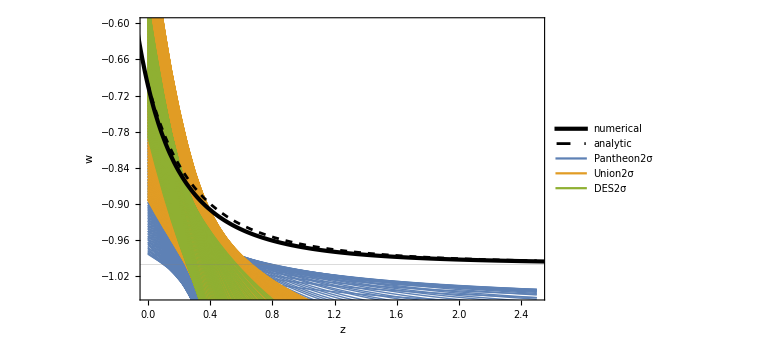

```mathematica
Show[Plot[{1,1,1,1,1},{x,0,1},PlotRange->{{0,2.5},{-1.05,-0.6}},FrameLabel->{z,w},PlotStyle->{{AbsoluteThickness[3],Black},{AbsoluteThickness[2],Black,Dashed},{Color[1]},{Color[2]},{Color[3]}},PlotLegends->Placed[LineLegend[{"numerical","analytic","Pantheon2σ","Union2σ","DES2σ"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.75,0.65}],GridLines->{None,{-1}},ImagePadding->pad],
Plot[Table[Drop[Pantheon2ssorted,-1][[i,1]]+Drop[Pantheon2ssorted,-1][[i,2]](1-1/(1+z)),{i,Length[Drop[Pantheon2ssorted,-1]]}],{z,0,2.5},PlotStyle->{Thin,Color[1]}],
Plot[Table[Drop[Union2ssorted,-1][[i,1]]+Drop[Union2ssorted,-1][[i,2]](1-1/(1+z)),{i,Length[Drop[Union2ssorted,-1]]}],{z,0,2.5},PlotStyle->{Thin,Color[2]}],
Plot[Table[Drop[DESY2ssorted,-1][[i,1]]+Drop[DESY2ssorted,-1][[i,2]](1-1/(1+z)),{i,Length[Drop[DESY1ssorted,-1]]}],{z,0,2.5},PlotStyle->{Thin,Color[3]}],
ParametricPlot[{zsol[t],wsol[t]},{t,0,tf},PlotStyle->{AbsoluteThickness[3],Black}],
Plot[w[1/(1+z)]/.{Ωϕ->7/10,KK->Sqrt[1-4/3 V''[xcs fs]/V[xcs fs]]}/.{f->fs,Λ2->Λ2s,w0->w0s},{z,0,2.5},PlotStyle->{AbsoluteThickness[2],Black,Dashed},PlotRange->Full]]
```

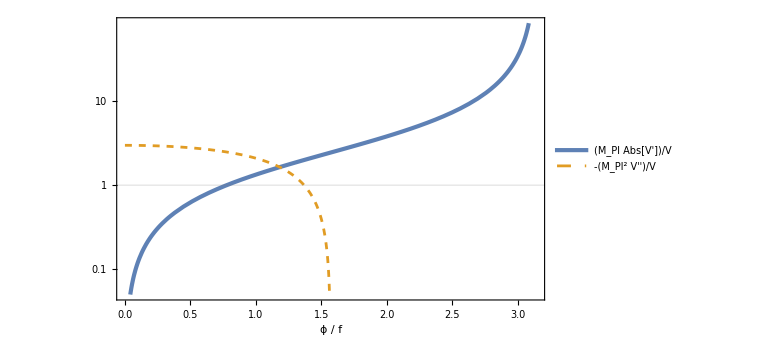

```mathematica
LogPlot[{Abs[V'[xc fs]]/V[xc fs]/.{f->fs,Λ2->Λ2s},-V''[xc fs]/V[xc fs]/.{f->fs,Λ2->Λ2s}},{xc,0,π},GridLines->{None,{1}},FrameLabel->{"ϕ / f",None},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[2],Dashed}},PlotLegends->Placed[LineLegend[{Subscript[M, Pl] Abs["V"']/V,-Subscript[M, Pl]^2"V"''/V},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.8,0.2}],ImagePadding->pad]
```

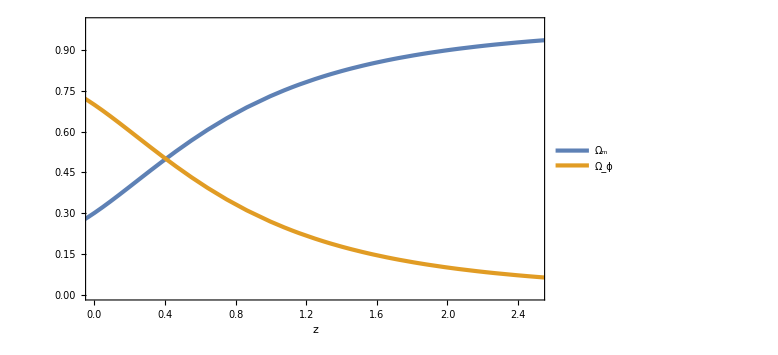

```mathematica
ParametricPlot[{{zsol[t],(Ωm(1+zsol[t])^3)/Hnorm[zsol[t],xsol[t],psol[t]]^2/.{f->fs,Λ2->Λ2s,Ωm->3/10}},{zsol[t],((psol[t]^2/2+V[xsol[t]])/3)/Hnorm[zsol[t],xsol[t],psol[t]]^2/.{f->fs,Λ2->Λ2s,Ωm->3/10}}},{t,0,tf},PlotRange->{{0,2.5},{0,1}},FrameLabel->{z,None},PlotLegends->Placed[{Subscript[Ω, "m"],Subscript[Ω, ϕ]},{0.8,0.5}]]
```

```mathematica
Hsol[t_]=H0rd Hnorm[zsol[t],xsol[t],psol[t]]/.{f->fs,Λ2->Λ2s,Ωm->3/10,H0rd->(*96.4*)100};
```

```mathematica
Hrd0=Import["Hrd0.csv"];
Hrd1p=Import["Hrd1p.csv"];
Hrd2p=Import["Hrd2p.csv"];
Hrd1m=Import["Hrd1m.csv"];
Hrd2m=Import["Hrd2m.csv"];
HrdLambda=Import["HrdLambda.csv"];
```

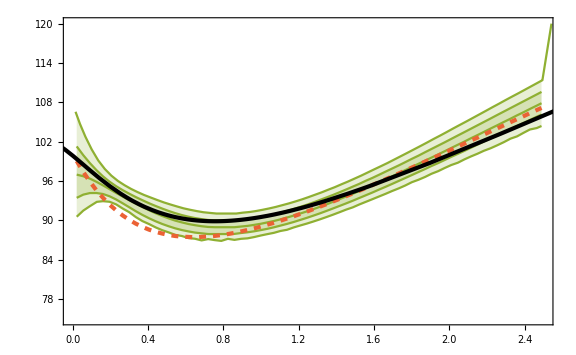

```mathematica
Show[ListPlot[{Hrd0,Hrd1p,Hrd2p,Hrd1m,Hrd2m},PlotStyle->Directive[Color[3]],Filling->{2->{4},3->{5}},PlotRange->{{0,2.5},{75,120}}],ListPlot[HrdLambda,PlotStyle->{AbsoluteThickness[3],Dashed,Color[4]}],
ParametricPlot[{zsol[t],Hsol[t]/(1+zsol[t])},{t,0,tf},PlotStyle->Directive[Black,AbsoluteThickness[3]]]]
```

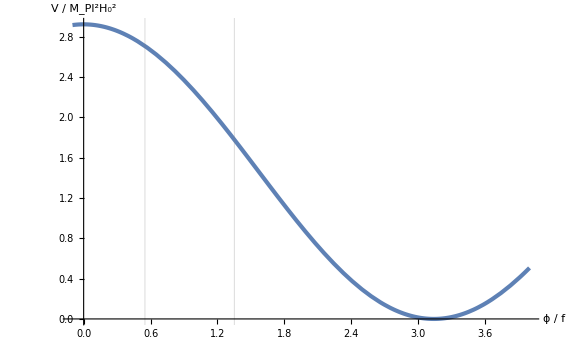

```mathematica
Plot[V[x f]/.{f->fs,Λ2->Λ2s},{x,-0.1,4},Frame->False,AxesStyle->Directive[Thick,Black],AxesLabel->{"ϕ / f","V / M_Pl^2H_0^2"},GridLines->{{xsol[0]/fs,xsol[t0]/fs},None}]
```